```mathematica
λ=0.725*I+4.15;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→0.428743+2.25121 ⅈ},{z→0.81651-2.66762 ⅈ},{z→1.19065+0.113922 ⅈ}}

0.428743+2.25121 ⅈ

0.81651-2.66762 ⅈ

1.19065+0.113922 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

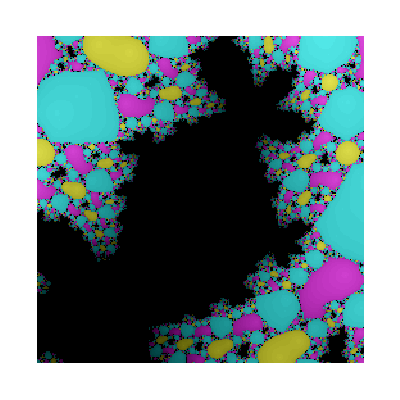

```mathematica
numberPoints =254;
limIterations=50;
xxMin=Re[z2]-1; xxMax=Re[z2]+1; yyMin=Im[z2]-1; yyMax=Im[z2]+1;
plotColorFractal[iterSch, numberPoints]
```

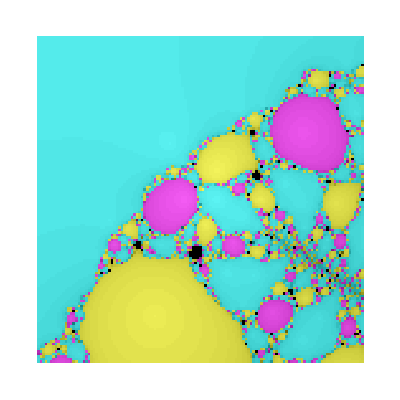

```mathematica
numberPoints =128;
limIterations=50;
xxMin=-10; xxMax=10; yyMin=-10; yyMax=10;
plotColorFractal[iterSch, numberPoints]
```

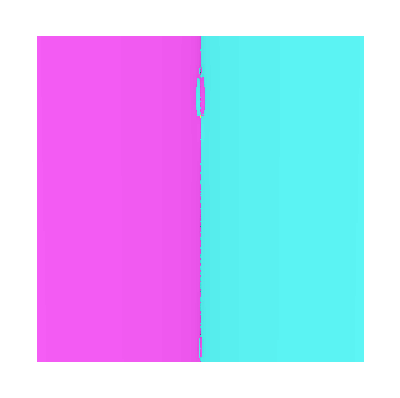

```mathematica
numberPoints =256;
limIterations=100;
xxMin=-0.25; xxMax=0.25; yyMin=0.25; yyMax=0.32;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
NestList[sp,z1,100]
```

{0.428743+2.25121 ⅈ,-0.208549-2.39708 ⅈ,-0.131098+1.72383 ⅈ,-0.858091-2.80347 ⅈ,-0.137214+1.34915 ⅈ,-2.43028-4.29451 ⅈ,0.261876+0.913717 ⅈ,3.56391+0.501463 ⅈ,3.92734+0.582334 ⅈ,4.12821+0.691668 ⅈ,4.15019+0.724215 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ,4.15+0.725 ⅈ}

```mathematica
NestList[sp,z2,100]
```

{0.81651-2.66762 ⅈ,0.173814+1.70189 ⅈ,-0.128836-2.92939 ⅈ,0.0399358+1.5682 ⅈ,-0.453332-3.46474 ⅈ,0.12235+1.39849 ⅈ,0.417962-4.32981 ⅈ,0.406039+1.49042 ⅈ,0.755743-2.66082 ⅈ,0.172934+1.70235 ⅈ,-0.131218-2.92935 ⅈ,0.0393911+1.56765 ⅈ,-0.455687-3.46733 ⅈ,0.122736+1.39758 ⅈ,0.425837-4.33461 ⅈ,0.407862+1.49142 ⅈ,0.752408-2.65403 ⅈ,0.172919+1.7026 ⅈ,-0.131522-2.92882 ⅈ,0.0391973+1.5677 ⅈ,-0.456568-3.46715 ⅈ,0.122587+1.39738 ⅈ,0.425815-4.33698 ⅈ,0.408325+1.49115 ⅈ,0.753465-2.65239 ⅈ,0.172977+1.70263 ⅈ,-0.131434-2.92868 ⅈ,0.0391848+1.56775 ⅈ,-0.456633-3.46692 ⅈ,0.122521+1.39739 ⅈ,0.425251-4.33727 ⅈ,0.408317+1.49101 ⅈ,0.75398-2.65244 ⅈ,0.172992+1.70262 ⅈ,-0.131392-2.92869 ⅈ,0.0391955+1.56776 ⅈ,-0.456586-3.46687 ⅈ,0.122515+1.39741 ⅈ,0.425117-4.33717 ⅈ,0.408283+1.491 ⅈ,0.754029-2.65257 ⅈ,0.172992+1.70262 ⅈ,-0.131388-2.9287 ⅈ,0.0391988+1.56775 ⅈ,-0.456571-3.46688 ⅈ,0.122519+1.39741 ⅈ,0.425124-4.33713 ⅈ,0.408275+1.491 ⅈ,0.754005-2.6526 ⅈ,0.17299+1.70262 ⅈ,-0.13139-2.9287 ⅈ,0.0391989+1.56775 ⅈ,-0.45657-3.46688 ⅈ,0.12252+1.39741 ⅈ,0.425135-4.33712 ⅈ,0.408276+1.491 ⅈ,0.753996-2.65259 ⅈ,0.17299+1.70262 ⅈ,-0.13139-2.9287 ⅈ,0.0391987+1.56775 ⅈ,-0.456571-3.46688 ⅈ,0.12252+1.39741 ⅈ,0.425137-4.33713 ⅈ,0.408276+1.491 ⅈ,0.753996-2.65259 ⅈ,0.17299+1.70262 ⅈ,-0.13139-2.9287 ⅈ,0.0391986+1.56775 ⅈ,-0.456571-3.46688 ⅈ,0.12252+1.39741 ⅈ,0.425137-4.33713 ⅈ,0.408277+1.491 ⅈ,0.753996-2.65259 ⅈ,0.17299+1.70262 ⅈ,-0.13139-2.9287 ⅈ,0.0391986+1.56775 ⅈ,-0.456571-3.46688 ⅈ,0.12252+1.39741 ⅈ,0.425137-4.33713 ⅈ,0.408277+1.491 ⅈ,0.753996-2.65259 ⅈ,0.17299+1.70262 ⅈ,-0.13139-2.9287 ⅈ,0.0391986+1.56775 ⅈ,-0.456571-3.46688 ⅈ,0.12252+1.39741 ⅈ,0.425137-4.33713 ⅈ,0.408277+1.491 ⅈ,0.753996-2.65259 ⅈ,0.17299+1.70262 ⅈ,-0.13139-2.9287 ⅈ,0.0391986+1.56775 ⅈ,-0.456571-3.46688 ⅈ,0.12252+1.39741 ⅈ,0.425137-4.33713 ⅈ,0.408276+1.491 ⅈ,0.753996-2.65259 ⅈ,0.17299+1.70262 ⅈ,-0.13139-2.9287 ⅈ,0.0391986+1.56775 ⅈ,-0.456571-3.46688 ⅈ}

```mathematica
NestList[sp,z3,100]
```

{1.15942+0.217111 ⅈ,1.00425-0.00436278 ⅈ,0.999995+8.08613×10^-6 ⅈ,1.+2.23916×10^-11 ⅈ,1.+7.62299×10^-23 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}